## Clustering Theory

```mathematica
Clear["Global`*"]
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx1024m"];
```

### Analyse the Voronoi area for each cell, as well as the Delaunay Network area

First take the data file with the xy coordinates (columns 8 and 9) of fluorescent cells
Then, perform Delaunay  triangulation, which is just the dual graph of the Voronoi Diagram for a set of points.
Delaunay triangulations maximize the minimum angle of all the angles of the triangles in the triangulation; they tend to avoid sliver triangles.
Then display the results in 3 plots, showing the coordinates (red point), tesselation (blue line) and both two together.

-Graphics-

-Graphics-

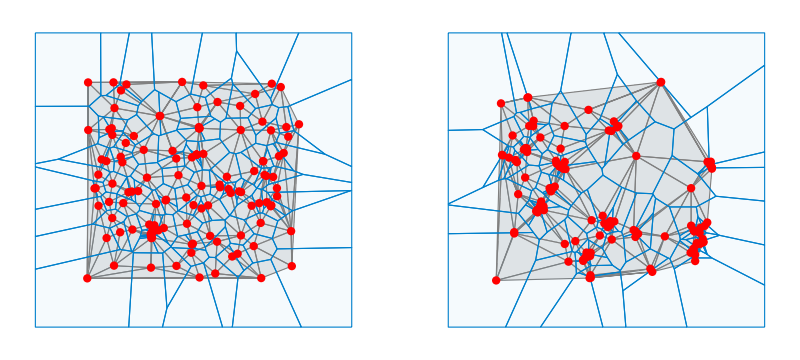

```mathematica
importFile = "/Users/mattesa/ZenBook/Code_Repository/To_Git/Mathematica/Analysis Pattern v_1/Test_dataset_1.xlsx";

xls1 = Import[importFile, {"Data",1,All,{8,9}}];
xls2 = Import[importFile, {"Data",2,All,{8,9}}];
delStyle={Style[0,{Red,PointSize[0.015]}],Style[1,Gray],Style[2,{LightGray,Opacity[0.6]}]};
vorStyle={Style[1,RGBColor[0,0.5,0.8]],Style[2,{RGBColor[0,0.5,0.8],Opacity[0.04]}]};

(* Define plotting styles *)
delaunay1=HighlightMesh[DelaunayMesh[xls1],delStyle];
voronoi1=HighlightMesh[VoronoiMesh[xls1],vorStyle];
delaunay2=HighlightMesh[DelaunayMesh[xls2], delStyle];
voronoi2=HighlightMesh[VoronoiMesh[xls2],vorStyle];

GraphicsRow[{Show[HighlightMesh[VoronoiMesh[xls1],{Style[2,{RGBColor[0,0.5,0.8],Opacity[0.1]}]}],Graphics[{Red,Point[xls1],PointSize[0.02]}]],
Show[HighlightMesh[VoronoiMesh[xls2],{Style[2,{RGBColor[0,0.5,0.8],Opacity[0.1]}]}],Graphics[{Red,Point[xls2],PointSize[0.02]}]]}]

GraphicsRow[{Show[HighlightMesh[DelaunayMesh[xls1],delStyle],Graphics[{Red,Point[xls1],PointSize[0.02]}]],
Show[HighlightMesh[DelaunayMesh[xls2],delStyle],Graphics[{Red,Point[xls2],PointSize[0.02]}]]}]


GraphicsRow[{Show[delaunay1,voronoi1],Show[delaunay2,voronoi2]}]
```

### Calculate the distibution of areas occupied by cells in the “network”

Now what we want is to assess and measure not just cell density but also the spread and closeness. 
We can use the tesselation area to calculate the area or territory occupied by one cell. We can then plot a distribution of the area and compare between them to assess the cell colonization density

Part::pkspec1: The expression x cannot be used as a part specification.

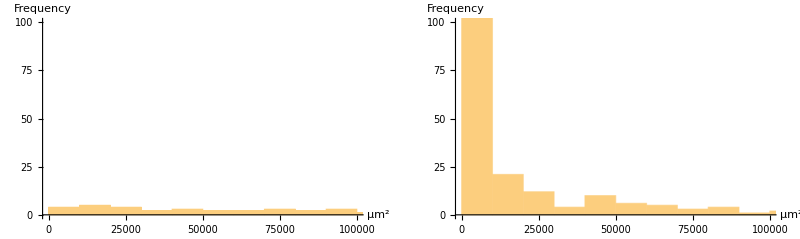

```mathematica
(* μm to pixel ratio is the following *)
um2px=0.164;
rng=200/um2px;

mReg1=DelaunayMesh[xls2];
polys1=MeshCells[mReg1,2]/.x_Integer->xls1[[x,{1,2}]];
polyArea1=(Area/@polys1)*um2px;

mReg2=DelaunayMesh[xls2];
polys2=MeshCells[mReg2,2]/.x_Integer->xls2[[x,{1,2}]];
polyArea2 = (Area/@polys2)*um2px;

(* Tell Wolfram Language what default text style to use for all subsequent Histogram plots. *)
SetOptions[Histogram,BaseStyle->{FontFamily->"Times",FontSize->14}];

GraphicsRow[ {Histogram[polyArea1,{10000},PlotRange->{{0,10^5},{0,100}},AxesLabel->{"μm^2","Frequency"}],Histogram[polyArea2,{10000},PlotRange->{{0,10^5},{0,100}}, AxesLabel->{"μm^2","Frequency"}]}]
```

### Calculate for each cell the distances to each neighbor that lies within a given radius from the cell (rng). Then calculate the distribution and draw the “general” distribution for the whole population.

Alternatively we can also assess cell distances between neighbouring cells (inspired by the machine learning algorithm k-mean) and count how many cells falls within a certain threshold value (rng).

```mathematica
um2px=0.164;
rng=200/um2px;

pDist1=Table[EuclideanDistance[xls1[[i]],xls1[[j]]],{i,1,Length[xls1]},{j,1,Length[xls1]}];
Map[Length,pDist1];
rngTable1=Table[Select[pDist1[[i]],0<#<rng&],{i,1,Length[pDist1]}];rngDistr1=Table[BinCounts[rngTable1[[i]],{0,rng,(rng/10)}],{i,1,Length[rngTable1]}];
D1=Total[rngDistr1,{1}]/Total[Total[rngDistr1]]//N
```

{0.0828221,0.0398773,0.0981595,0.0766871,0.0889571,0.0766871,0.095092,0.144172,0.150307,0.147239}

```mathematica
pDist2=Table[EuclideanDistance[xls2[[i]],xls2[[j]]],{i,1,Length[xls2]},{j,1,Length[xls2]}];Map[Length,pDist2];
rngTable2=Table[Select[pDist2[[i]],0<#<rng&],{i,1,Length[pDist2]}];rngDistr2=Table[BinCounts[rngTable2[[i]],{0,rng,(rng/10)}],{i,1,Length[rngTable2]}];
D2=Total[rngDistr2,{1}]/Total[Total[rngDistr2]]//N
```

{0.0915594,0.135908,0.110157,0.055794,0.0600858,0.0701001,0.0987124,0.108727,0.121602,0.147353}

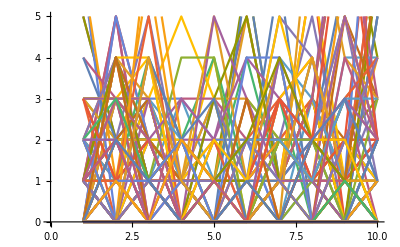

```mathematica
ListLinePlot[rngDistr2]
```

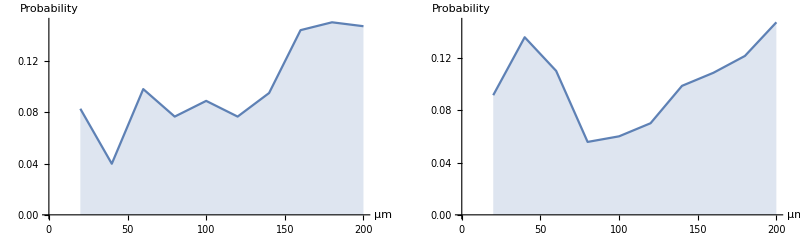

```mathematica
X=Range[(rng/10)*um2px,rng*um2px,(rng/10)*um2px];GraphicsRow[{ListLinePlot[Transpose[{X,D1}],Filling->Axis,AxesLabel->{"μm","Probability"},BaseStyle->{FontFamily->"Times",FontSize->16}],ListLinePlot[Transpose[{X,D2}],Filling->Axis,AxesLabel->{"μm","Probability"},BaseStyle->{FontFamily->"Times",FontSize->16}]}]
```

### Calculate for each cell the distances to each neighbor and select the smallest/nearer one. Plot distribution of the nearest neighbor distance.

Alternatively we can calculate the distance to the closest N neighbours and plot this as a distribution. Somewhat related to area occupied, but should capture better if cells are clustering in small group, and at the same time the groups are distant to each other.
NOTE: This step can be quite computationally intense

```mathematica
um2px=0.164;
rng=200/um2px;

pDist1=Table[EuclideanDistance[xls1[[i]],xls1[[j]]],{i,1,Length[xls1]},{j,1,Length[xls1]}]*um2px;
Distr1=Table[RankedMin[pDist1[[i]],2],{i,1,Length[pDist1]}];

pDist2=Table[EuclideanDistance[xls2[[i]],xls2[[j]]],{i,1,Length[xls2]},{j,1,Length[xls2]}]*um2px;
Distr2=Table[RankedMin[pDist2[[i]],2],{i,1,Length[pDist2]}];

GraphicsRow[{Histogram[Distr1,{rng/10*um2px},"Probability",PlotRange->{{0,rng*um2px},{0,1}},AxesLabel->{"μm","Probability"}],Histogram[Distr2,{rng/10*um2px},"Probability",PlotRange->{{0,rng*um2px},{0,1}},AxesLabel->{"μm","Probability"}]}]
```

RankedMin::intm: Machine-sized integer expected at position RankedMin[{0.,0.164 √(Abs[Plus[«2»]]^2+Abs[Plus[«2»]]^2),0.164 √(Abs[Plus[«2»]]^2+Abs[Plus[«2»]]^2),0.164 √(Abs[Plus[«2»]]^2+Abs[Plus[«2»]]^2),«43»,0.164 √(Abs[Plus[«2»]]^2+Abs[Plus[«2»]]^2),0.164 √(Abs[Plus[«2»]]^2+Abs[Plus[«2»]]^2),0.164 √(Abs[Plus[«2»]]^2+Abs[Plus[«2»]]^2),«100»},2.] in 2.

RankedMin::intm: Machine-sized integer expected at position RankedMin[{0.164 √(Abs[Plus[«2»]]^2+Abs[Plus[«2»]]^2),0.,314.368,507.86,871.585,934.491,926.769,899.776,«36»,999.493,1097.92,1465.33,1213.56,1646.,285.46,«100»},2.] in 2.

RankedMin::intm: Machine-sized integer expected at position RankedMin[{0.164 √(Abs[Plus[«2»]]^2+Abs[Plus[«2»]]^2),314.368,0.,369.904,637.337,711.37,700.041,627.893,«36»,692.247,803.372,1199.02,902.876,1394.36,450.08,«100»},2.] in 2.

General::stop: Further output of RankedMin::intm will be suppressed during this calculation.

-Graphics-

### Find the distributions of distances in the Delanunay network.

Part::pkspec1: The expression x cannot be used as a part specification.

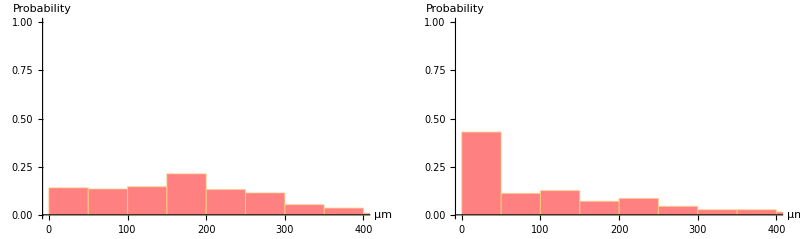

```mathematica
(* Get the Lines of the network *)
ln1=Map[ArcLength, MeshCells[ DelaunayMesh[xls1],1] /.x_Integer->xls1[[x,{1,2}]]]*um2px;
ln2=Map[ArcLength, MeshCells[ DelaunayMesh[xls2],1] /.x_Integer->xls2[[x,{1,2}]]]*um2px;

GraphicsRow[{Histogram[ln1,{50},"Probability",PlotRange->{{0,400},{0,1}},AxesLabel->{"μm","Probability"},ChartStyle->{RGBColor[1,0.5,0.5]}],Histogram[ln2,{50},"Probability",PlotRange->{{0,400},{0,1}},AxesLabel->{"μm","Probability"},ChartStyle->{RGBColor[1,0.5,0.5]}]}]
```